## Елисеев С. Г.

## Лабораторная работа №1 : Списки. Строки и текст

## 1.1

### 1. Используя функцию Range создайте список {1,2,3,4}

```mathematica
Range[4](* Создаёт список чисел{1,2,3,4} *)
```

### 2. Создайте список из натуральных чисел от 1 до 100

```mathematica
Range[100](* Создаёт список из натуральных чисел (числа, получающиеся естественным образом при счёте) от 1 до 100 *)
```

### 3. Используя функции Range и Reverse, создайте список {4, 3, 2, 1}

```mathematica
Reverse[Range[4]](* Создаёт список {1, 2, 3, 4} и переворачивает его, в результате получаем {4, 3, 2, 1} *)
```

{4,3,2,1}

### 4. Создайте список из натуральных чисел от 1 до 50 в обратном порядке

```mathematica
Reverse[Range[50]](* Создаёт список натуральных чисел (числа, получающиеся естественным образом при счёте) {1, 2,..., 49, 50} и меняет порядок на обратный*)
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
5.Используя функции Range,Reverse и Join,создайте список {1,2,3,4,4,3,2,1}
```

Syntax::tsntxi: "5.ИспользуяфункцииRange,ReverseиJoin,создайтесписок{1,2,3,4,4,3,2,1}" is incomplete; more input is needed.

```mathematica
Join[Range[4],Reverse[Range[4]]](* Создаёт список {1, 2, 3, 4,} дважды, в одном списке меняет порядок на обратный и затем объединяет полученные списки, ожидаем: {1,2,3,4,4,3,2,1} *)
```

```mathematica
6. Нарисовать график списка чисел,которые возрастают от 1 до 100,а затем убывают от 100
до 1
```

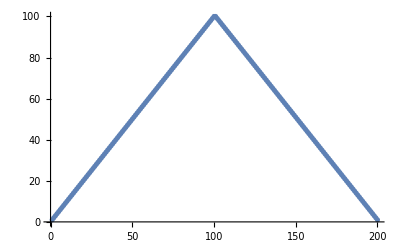

```mathematica
ListPlot[Join[Range[100],Reverse[Range[100]]]](* Рисует график от 1 до 100, а затем от 100 до 1 *)
```

```mathematica
7. Используя функции Range и RandomInteger создайте список случайно генерированной
длины,не превышающей число 10
```

```mathematica
Range[RandomInteger[10]](* Создаёт список случайно генерированной длины, с максимальным числом 10 *)
Range[RandomInteger[{0,10}]](* Создаёт список случайно генерированной длины, где 0 - минимально возможное,а 10 - максимально возможное значение *)
```

{}

{1,2,3,4,5,6}

```mathematica
8.  Найти простейшую форму для команды Reverse[Reverse[Range[10]]]
```

```mathematica
Range[10](* Два раза поменяв порядок мы получим, тоже значение, что и не выполняя дважды команду Reverse след. простейшую форму команды Reverse[Reverse[Range[10]]] получим убрав команды Reverse *)
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
9. Найти простейшую форму для команды Join[{1,2},Join[{3,4},{5}]]
```

```mathematica
Range[5](* {1,2}+{3,4} + {5}, простейшая форма команды Join[{1,2},Join[{3,4},{5}]] будет выводом списка чисел от 1 до 5 - Range[5]*)
```

{1,2,3,4,5}

```mathematica
10. Найти простейшую форму для команды Join[Range[10],Join[Range[10],Range[5]]]
```

```mathematica
Join[Range[10],Range[10],Range[5]](* {1, 2,...,10} + ({1,...,10} + {1,...,5}), простейшая форма команды Join[Range[10],Join[Range[10],Range[5]]] будет объединением этих списком, т.е. следует удбрать второй Join *)
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

```mathematica
11.Найти простейшую форму для команды Reverse[Join[Range[20],Reverse[Range[20]]]]
```

```mathematica
Join[Range[20],Reverse[Range[20]]](* Первый Reverse, лишний, т.к. он поменят порядок чисел списков, тем самым вернёт порядо к одного из них в исходный *)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
Reverse[Join[Range[20],Reverse[Range[20]]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

## 1.2 Строки и текст (Strings and Text)

### 1. Присоедините две копии строки «Здравствуйте».

```mathematica
StringJoin["Здравствуйте","Здравствуйте"](*Соединяет две строки*)
```

ЗдравствуйтеЗдравствуйте

### 2. Создайте единую строку всего английского алфавита заглавными буквами

```mathematica
ToUpperCase[Alphabet[]](*Создаёт англ. алфавит и преводит его к верхнему регистру*)
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

### 3. Сгенерируйте строку английского алфавита в обратном порядке

```mathematica
Reverse[Alphabet[]](*Показывает алфавит в обратном порядке, английский по умолчанию*)
```

{z,y,x,w,v,u,t,s,r,q,p,o,n,m,l,k,j,i,h,g,f,e,d,c,b,a}

### 4. Объедините 100 копий строки «ABCD»

```mathematica
StringJoin[StringRepeat["ABCD",100]](*Создаёт сто копий строки и соединяет их*)
```

ABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCD

### 5. Используйте StringTake, StringJoin и Alphabet, чтобы получить «abcdef»

```mathematica
StringTake[StringJoin[Alphabet[]],6](*Создаём алфавит, объеденяем строки и берём первые 6 значений*)
```

abcdef

### 6. Создайте столбец с числом элементов, равных длине строки «это о строках» и содержащих число букв (включая пробелы) равное номеру элемента

```mathematica
Column[Table[StringTake["это о строках", n], {n, StringLength["это о строках"]}]](*Создаём таблицу, где stringtake - значения таблицы(n+1), stringlenght - наша длинна, затем получаем список, который приведём к виду колонки*)
```

э
эт
это
это 
это о
это о 
это о с
это о ст
это о стр
это о стро
это о строк
это о строка
это о строках

### 7. Создайте гистограмму длин слов в «Давным-давно, в далекой галактике, далеко».

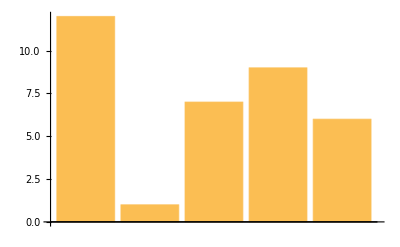

```mathematica
BarChart[StringLength[TextWords["Давным-давно, в далекой галактике, далеко"]]](*Создаём список со значениями длин слов и создаём гистограму из полученных знач.*)
```

### 8. Найдите максимальную длину слова среди английских слов из WordList []

```mathematica
Max[StringLength[WordList[]]](*Получаем список из простых слов, затем получаем длинну для каждого и находим маскимальное значение из списка*)
```

21

### 9. Используйте Length, чтобы найти длину русского алфавита

```mathematica
Length[Alphabet["Russian"]](*Создаём русских алфавит и находим длинну*)
```

33

### 10. Создайте строку из заглавных букв греческого алфавита в обратном порядке.

```mathematica
ToUpperCase[StringJoin[Reverse[Alphabet["Greek"]]]](*Создал греческий алфавит, перевернул его, затем соединил значения и превёл их к верхнему регистру*)
```

ΩΨΧΦΥΤΣΡΠΟΞΝΜΛΚΙΘΗΖΕΔΓΒΑ

## 1.3 Чистые функции

```mathematica
1. Используйте Range и чистую функцию для создания списка из квадратов первых 20
натуральных чисел
```

```mathematica
#^2&/@Range[20](*# - слот, указывает,куда поместить каждый элемент,когда применяется чистая функция, /@ - применяет чистую функцию к каждому элементу в списке*)
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
2. Составьте список из результатов смешивания желтого,зеленого и синего цветов с красным
цветом
```

```mathematica
Blend[{#,Red},1/2]&/@{Yellow,Green,Blue}(*Чистая функция для составления списка смешивания цветов*)
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

```mathematica
3. Создайте список столбцов в рамках,содержащих прописные и строчные версии каждой
буквы алфавита
```

```mathematica
Framed[Column[{ToUpperCase[#],#}]]&/@Alphabet[](*Список столбцов в рамках, который содержит прописные и строчные версии каждой буквы алфавита*)
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
4. Составьте список букв алфавита в случайных цветах в рамках,имеющих случайные цвета
фона
```

```mathematica
Framed[Style[#,RandomColor[]], Background->RandomColor[]]&/@Alphabet[](*Список букв алфавита в случайных цветах в рамках,имеющих случайные цвета фона*)
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
5.Напишите в более простой форме команду (#^2+1&)/@Range[10]
```

```mathematica
Range[10]^2+1(*Каждое число из списка, созданного Range, возводим в квадрат и прибавлем 1, получаем упрощенную форму команды (#^2+1&)/@Range[10]: Range[10]*2 + 1*)
```

{2,5,10,17,26,37,50,65,82,101}

## 1.4 Композиции функций и их программирование

```mathematica
1. Составьте список результатов использования функции Blur до 10 раз начиная с
растрированного размера 30 “X” (Используйте:Rasterize[Style)
```

```mathematica
NestList[Blur,Rasterize[x,RasterSize->30],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
2. Начните с x,затем создайте список,использовав последовательно функцию Framed до 10
раз,используя каждый раз случайный цвет фона
```

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10](*Список, созданный с помощью последовательного использования функции Framed до 10 раз*)
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
3. Начните с размера 50 для “A”,затем создайте список вложенного применения Framed и случайного вращения 5 раз
```

Syntax::tsntxi: "3.Начнитесразмера50для“A”,затемсоздайтесписоквложенногопримененияFramedислучайноговращения5раз" is incomplete; more input is needed.

```mathematica
NestList[Rotate[Framed[#],Pi*Random[]]&,Style["A",FontSize->50], 5](*Список вложенного применения Framed, в котором случайно вращаются фрэймы(5 раз)*)
```

{A,A,A,A,A,A}

```mathematica
4. Создайте линейный график из 100 итераций логического итерационного отображения 4 #(1-#)&,начиная с 0.2
```

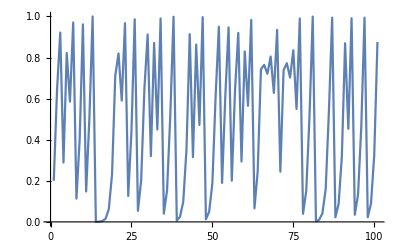

```mathematica
ListLinePlot[NestList[4 #(1-#)&,0.2,100]](*Линейный график из 100 итераций логического итерационного отображения 4#(1-#)&, начиная с 0.2*)
```

```mathematica
5. Найдите числовое значение результата из 30 итераций применения функции 1+1/#&,начиная с 1
```

```mathematica
Nest[1+1/#&,1,30](*Функция для получения числового значения результата из 30 итераций функции 1+1/#&, начиная с 1*)
```

2178309/1346269

```mathematica
6. Создайте список из первых 10 степеней 3 (начиная с 0) путем вложенного умножения
```

```mathematica
NestList[3*#&,1,10](*Cписок из первых 10 степеней 3*)
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

```mathematica
7. Составьте список результатов действия вложенной функции (метод Ньютона) (#+2/#)/2 до
5 раз,начиная с 1.0 ,  а затем вычтите 2 из всех результатов
```

```mathematica
NestList[(#+2/#)/2-Sqrt[2]&,1.0,5](*Список результатов метода Ньютона(итерационный численный метод нахождения корня заданной функции) для вложенной функции*)
```

{1.,0.0857864,10.2855,3.82578,0.76006,0.281502}

```mathematica
8. Создайте список из 5 степеней числа 2,т.е.2^2^2...^2 n раз,причем n меняется от 0 до 4
```

```mathematica
NestList[#^2&,Table[2,1],5](*Список из 5 степеней числа 2*)
```

{{2},{4},{16},{256},{65536},{4294967296}}

## 1.5 Определение функций пользователя

```mathematica
1. Определите функцию f,которая вычисляет квадрат ее аргумента
```

```mathematica
f[x_]:=x^2;(*x_ - слева от символа подчёркивания находится имя образца, имеет тип Symbol*)
f[4]
```

16

```mathematica
2. Определите функцию poly,которая имеет целочисленное значение аргумента и создает
изображение оранжевого правильного многоугольника с числом сторон,равным значению
этого аргумента
```

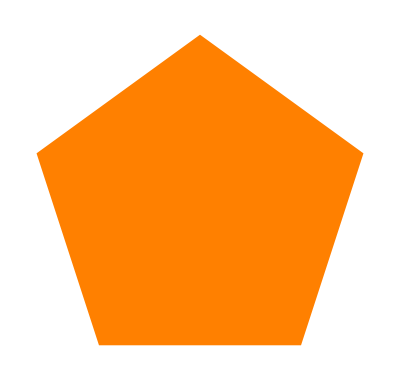

```mathematica
poly[x_]:=Graphics[{Orange,Polygon[CirclePoints[x]]}];(*Определил функцию poly, кот создаёт прав многоугольник с кол сторон == аргументу*)
poly[5]
```

```mathematica
(* или можно с помощью функции RegularPolygon*)
poly[x_]:= Graphics[{Orange, RegularPolygon[x]}];
poly[5]
```

-Graphics-

```mathematica
3. Определите функцию f,которая берет список из двух элементов и помещает их в обратном
порядке
```

```mathematica
f[{x_,y_}]:=Reverse[{x,y}];(*Функция, берущая список из 2-х элементов и выводящая их в обратном порядке*)
f[{2,3}]
```

{3,2}

```mathematica
4. Определите функцию f,которая имеет два аргумента и дает результат в виде дроби,где
числитель равен произведению этих элементов,а знаменатель-их сумме
```

```mathematica
f[x_,y_]:= (x*y)/(x+y);(*Функция, принимающая 2 аргумента и возвращающая результат в виде дроби, где числитель - произведение аргументов, а знаминатель - их сумма*)
f[2,3]
```

6/5

```mathematica
5. Определите функцию f,которая имеет два аргумента и дает результат в виде списка трех
элементов,которые соответственно равны сумме,разности и частному этих аргументов
```

```mathematica
f[x_,y_]:={x+y,x-y,x/y};(*Функция, возвращающая список из трёх аэлементов, где первый - сумма арг, второй - разница и третиц - частное аргументов*)
f[2,3]
```

{5,-1,2/3}

```mathematica
6. Определите функцию evenodd,которая зависит от одного целочисленного аргумента и
имеет значение Black,если ее аргумент четный,значение-White в противном случае,значение
Red-если аргумент равен нулю.
```

```mathematica
evenodd[0]:=Red;
evenodd[x_]:= If[EvenQ[x], Black,White];(*Функция, в которой если аргумент нечетный, то значение на выходе white, red - равен нулю, black - четный*)
evenodd[2]
```

GrayLevel[0]

```mathematica
7. Определите функцию Fibonacci f с f[0]=1 и f[1]=1,а f[n] для натурального числа n является
суммой f[n-1] и f[n-2]
```

```mathematica
f[0]:=1;
f[1]:=1;
f[x_]:=f[x-1]+f[x-2];(*Функцию Фибоначчи*)
f[60]
```

8

```mathematica
Fibonacci[60]
```

8